```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]
fs=Style[#,FontSize->14]&;

<<MaTeX`

SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

/Users/pjoot/project/figures/phy452-basicstatmech

```mathematica
Clear[z,el, u, cv, zSmallTimeApprox, uNumeratorSmallTimeApprox, uSmallTimeApprox]

(* u = e_0/tau *)
el[u_, l_] = Exp[-l(l+1)u] ;
z[u_, lmax_] := Sum[ (2l+1) el[u, l],{l,0,lmax}] 
(* syntax wrong.  partial not being evaluated before subst of t ... how to fix? *)
 (*u[e_, t_, lm_] := t^2 D[Log[ z[e/t, lm] ], t]*)

u[e_, t_, lmax_] := e Sum[ l(l+1)(2l+1) el[e/t, lmax] ,{l,1,lmax}] /z[e/t, lmax]  
cv[e_, t_, lmax_] := (e/t)^2(
Sum[ l^2(l+1)^2(2l+1)el[e, l],{l,1,lmax}] /z[e/t, lmax] 
+ (u[e, t, lmax]/e)^2
)

zSmallTimeApprox[e_, t_] = Integrate[ (2l + 1)el[e/t, l] , {l, 0, Infinity}] ;
uNumeratorSmallTimeApprox[e_, t_] = Integrate[ l (l+1)(2l + 1)el[e/t, l] , {l, 1, Infinity}] ;
uSmallTimeApprox[e_, t_] = e  FullSimplify[ uNumeratorSmallTimeApprox[e, t]/zSmallTimeApprox[e, t], e> 0 && t > 0]
```

Integrate::ilim: Invalid integration variable or limit(s) in {π,0,∞}.

Integrate::ilim: Invalid integration variable or limit(s) in {π,1,∞}.

Integrate::ilim: Invalid integration variable or limit(s) in {π,0,∞}.

(e ∫_1^∞ ⅇ^(-(e π (1+π))/t) π (1+π) (1+2 π)ⅆπ)/(∫_0^∞ ⅇ^(-(e π (1+π))/t) (1+2 π)ⅆπ)

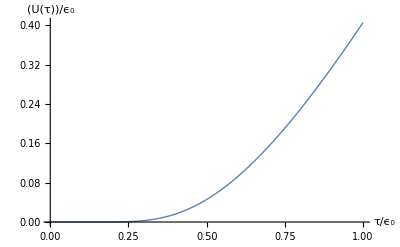

```mathematica
kittelRotationalPartitionFig6 = Plot[
uSmallTimeApprox[1, t], {t, 0, 1},
AxesLabel->{τ/Subscript[ϵ, 0] //fs, U[τ]/Subscript[ϵ, 0]// fs},
PlotStyle->Thick]
```

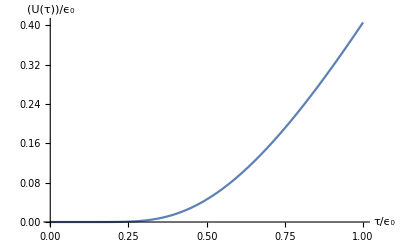

-Graphics3D-

-Graphics3D-

```mathematica
Manipulate[
LogLinearPlot[ 
z[u, lm],
 {u, 0.00001, 1000},
 AxesLabel -> {Subscript[ϵ, 0]/τ, Z[Subscript[ϵ, 0]/τ]},
PlotRange-> Full
],
{{lm, 30},0,30, 1}
]

Manipulate[
LogLinearPlot[ 
z[u, lm],
 {u, 0.00001, 1000},
 AxesLabel -> {Subscript[ϵ, 0]/τ, Log[Z[Subscript[ϵ, 0]/τ]]},
PlotRange-> Full
],
{{lm, 30},0,30, 1}
]

Manipulate[
LogLinearPlot[ 
cv[1, t, lm], 
{t, 0.1, 10}, 
AxesLabel -> {Subscript[ϵ, 0]/τ, Subscript[C, v][τ]/(Subscript[ϵ, 0])^2} (*, 
PlotRange -> {{0, 100},{0, 3}}*)
],{{lm, 30},0,30, 1}]


(*Plot[ 
u[1, t, 10], 
{t, 0.001, 0.5}, 
AxesLabel -> {Subscript[ϵ, 0]/τ, U[τ]/e} ,
PlotRange -> Full
]
*)

Plot3D[ 
(2 l + 1) el[1/t, l], 
{t, 0, 100}, 
{l, 0, 40}, 
AxesLabel->{τ/Subscript[ϵ, 0], l, (2 l + 1)E^(-l(l+1)Subscript[ϵ, 0]/τ)}, 
PlotRange -> Full] 

Plot3D[ 
(2 l + 1) l^2 (l+1)^2 el[1/t, l],
{t, 0, 1}, 
{l, 0, 40}, 
AxesLabel->{τ/Subscript[ϵ, 0], l, (2 l + 1)E^(-l(l+1)Subscript[ϵ, 0]/τ)}, 
PlotRange -> Full] 

Manipulate[
LogLinearPlot[ 
u[1, t, lm], 
{t, 10, 60}, 
AxesLabel -> {Subscript[ϵ, 0]/τ, U[τ]/Subscript[ϵ, 0]} 
],{{lm, 30},0,30, 1}]
```

```mathematica
kittelRotationalPartitionFig7 = DynamicModule[{lm=30},
LogLinearPlot[cv[1,t,lm],{t,0.1,10},
PlotStyle->{Thick,Black},
AxesLabel->{
(*Subscript[ϵ, 0]/τ//fs,
(Subscript[C, v][τ])/Subscript[ϵ, 0]^2 // fs*)
MaTeX["\\epsilon_0/\\tau"],
MaTeX["Z_R(\\tau)"]
}]]
```

```mathematica
kittelRotationalPartitionFig5 = DynamicModule[{lm=30},LogLinearPlot[u[1,t,lm],{t,10,60},AxesLabel->{Subscript[ϵ, 0]/τ,U[τ]/Subscript[ϵ, 0]}, PlotStyle->Thick]]
```

```mathematica
kittelRotationalPartitionFig2 = DynamicModule[{lm=30},LogLinearPlot[z[u,lm],{u,0.00001,1000},AxesLabel->{Subscript[ϵ, 0]/τ,"Z_R(τ)"},PlotRange->Full, PlotStyle->Thick]]
```

```mathematica
peeters`exportForLatex["kittelRotationalPartitionFig2",kittelRotationalPartitionFig2]
```

{kittelRotationalPartitionFig2.eps,kittelRotationalPartitionFig2pn.png}

```mathematica
peeters`exportForLatex["kittelRotationalPartitionFig5",kittelRotationalPartitionFig5]
```

{kittelRotationalPartitionFig5.eps,kittelRotationalPartitionFig5pn.png}

```mathematica
peeters`exportForLatex["kittelRotationalPartitionFig6",kittelRotationalPartitionFig6]
```

{kittelRotationalPartitionFig6.eps,kittelRotationalPartitionFig6pn.png}

```mathematica
peeters`exportForLatex["kittelRotationalPartitionFig7",kittelRotationalPartitionFig7]
```

{kittelRotationalPartitionFig7.eps,kittelRotationalPartitionFig7pn.png}